## Calculation

```mathematica
wp=50;(* Working precision *)
ag=25;(* Accuracy goal *)
pg=25;(* Precision goal *)
q = Sqrt[2];
phiDEQ = ((-k^2 (-1+u) (-1+u (-1+q^2 u))+w^2) phi[u])/(4 (-1+u)^2 u (1+u-q^2 u^2)^2)+((-1+u (-1+q^2 u)) (-1+u^2 (-1+q^2 (-1+2 u))) phi'[u])/((-1+u) u (1+u-q^2 u^2)^2)+((-1+u (-1+q^2 u))^2 phi''[u])/((1+u-q^2 u^2)^2);
```

Extremal horizon expansion

```mathematica
order=40;
coefficients =Get["/home/finn/Documents/studienprojekt/ruleExt40"];
phiSeries[u_]:=  E^(-I w/(6 ( 1- u))) * (1-u)^(7 I w/36)* Sum[h[nn] (1-u)^nn, {nn, 0, order}];
horizonExpansion[u_] :=SetPrecision[phiSeries[u] /. coefficients /. {h[0]->1, h[order]->0},wp]
```

```mathematica
(*Table[ SetPrecision[ E^(-I w/(6 ( 1- u))) * (1-u)^(7 I w/36)* Sum[h[nn] (1-u)^nn, {nn, 0, i}]/.coefficients/.{h[0]->c0,h[order]->0}/.{c0->1, u->0.999, w->1/10, k->1/10},wp],{i,1,40}] *)
```

Solve DEQ

```mathematica
epsilon=1/1000000000; uBnum=epsilon;uHnum=1-1/1000;

Clear[solphi]
solphi[omega_?NumericQ,kay_,c0_]:=
Block[
{w=omega,k=kay},
Print["Shear Mode for omega: ", N[omega,wp], " k: ", N[kay,3]];
	NDSolve[
	{0==phiDEQ,
	phi[uHnum]==horizonExpansion[uHnum],
		phi'[uHnum]==(D[horizonExpansion[u],u]/.{u->uHnum})
		},
		phi[u],{u,uBnum,uHnum},
		WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg,MaxSteps->1000000
]
]

(* Usage: phiSol(w, k) *)
phiSol[w_?NumericQ, k_]:=SetPrecision[solphi[w,k,1][[1,1,2]],wp]
```

Shear Mode for omega: -0.2 ⅈ k: 0

NDSolve::precw: The precision of the differential equation ({{0==-phi[u]/(100 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==2.55003511804738378194781935516093188643642478043×10^-15,phi'[999/1000]==-8.50985772210467473117876749124175255540381787×10^-11},{},{},{},{}}) is less than WorkingPrecision (50.).

0.8570276513881871656645404382521875641009678678709

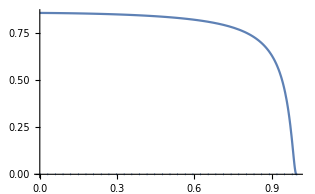

```mathematica
sol = phiSol[0-20/100*I, 0];
sol /. u->(uBnum) // Print;
ReImPlot[phi[u] /.{phi[u] -> sol}, {u, uBnum, uHnum}]
```

```mathematica
(*dataReal= Table[SetPrecision[{a,b,Re[phiSol[a+I*b, 1.0]]}/.u->uBnum,wp],{a, 8/100, 10/100,10/100},{b,-10/100,-1/2000,1/200}];*)
(*dataImag= Table[SetPrecision[{a,b,Tanh[Im[phiSol[a+I*b, 1/2]]]}/.u->uBnum,wp],{a, 3/100, 7/100,5/1000},{b,-16/1000,-12/1000,1/1000}];*)


(*dataReal= Table[SetPrecision[{a,b,Tanh[Re[phiSol[a+I*b, 1/2]]]}/.u->uBnum,wp],{a,4/100,2,1/4},{b,-2,-1/100,1/4}];*)
(*dataImag= Table[SetPrecision[{a,b,Tanh[Imag[phiSol[a+I*b, 1/2]]]}/.u->uBnum,wp],{a,4/100,2,1/4},{b,-2,-1/100,1/4}];*)
```

```mathematica
ListPointPlot3D[dataReal]
(*ListPointPlot3D[dataImag]*)
```

-Graphics3D-

```mathematica
qnmRoutine[initWR_,initWI_,kay_,kuh_]:=Block[
{iWR=initWR,iWI=initWI,k=kay,q=kuh},
eqQNMVBC[wR_?NumericQ,wI_?NumericQ]:=SetPrecision[Block[{w=wR+ⅈ wI},solution=phiSol[w,k]/.u->uBnum; Print[solution]; Return[solution]],wp];
findQNMVBC[reWi_?NumericQ,imWi_?NumericQ]:=
FindRoot[
{
Re[eqQNMVBC[wr,wi]]==0,
Im[eqQNMVBC[wr,wi]]==0},
{wr,reWi},{wi,imWi},
WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg,
Method->"Newton",
MaxIterations->1000
];
qnmVBC=SetPrecision[findQNMVBC[iWR,iWI],wp];
Print[{qnmVBC[[1,2]],qnmVBC[[2,2]]}]
]
```

```mathematica
phiSol[0.08883656535123935-0.03503410078638751*I, 1]/. u->(uBnum) // Print
```

Shear Mode for omega: 0.0888366-0.0350341 ⅈ k: 1.

NDSolve::precw: The precision of the differential equation ({{0==(((0.00666455-0.00622462 ⅈ)-Plus[«2»] Plus[«2»]) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==-0.0019750562972462972280429660543177305953577160835266-0.001954488476469308337601926695015208679251372814178 ⅈ,phi'[999/1000]==-17.421002565265191909058257834862669358990095+40.6986348119243089712069963675458534444225622 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

1.292366071045931837710131239091004643245893378677-0.211516950043542495396867407817004894401737699781 ⅈ

k: 0.8
0.741437-0.722166 ⅈ k: 0.9
0.658371-0.725126 ⅈ k: 1

```mathematica
qnmRoutine[7ⅇ^(-11),-7/1000,1/100, Sqrt[2]]
```

Shear Mode for omega: 0.000116911905531719615188448621524066153545566328715-0.007 ⅈ k: 0.01

NDSolve::precw: The precision of the differential equation ({{0==(((-0.00004898633160634494226844217732614984296328230345266-1.63676667744407461263828070133692614963792860201×10^-6 ⅈ)-(Plus[«2»] Plus[«2»])/10000) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==-«87»+«88» ⅈ,phi'[999/1000]==3.77384266911780332048898395968602432259118115×10^31-2.89575641269176564660342834441556567052697654×10^31 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

-4.868217273747466432431743113502242144316739760824×10^28+3.679559659517495477465728411428649272957666967174×10^28 ⅈ

Shear Mode for omega: 0.000116911905531719615188448621524066153545566328715-0.007 ⅈ k: 0.01

NDSolve::precw: The precision of the differential equation ({{0==(((-0.00004898633160634494226844217732614984296328230345266-1.63676667744407461263828070133692614963792860201×10^-6 ⅈ)-(Plus[«2»] Plus[«2»])/10000) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==-«87»+«88» ⅈ,phi'[999/1000]==3.77384266911780332048898395968602432259118115×10^31-2.89575641269176564660342834441556567052697654×10^31 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

-4.868217273747466432431743113502242144316739760824×10^28+3.679559659517495477465728411428649272957666967174×10^28 ⅈ

Shear Mode for omega: 0.000116911905531719615188448621524066153545566328715-0.007 ⅈ k: 0.01

NDSolve::precw: The precision of the differential equation ({{0==(((-0.00004898633160634494226844217732614984296328230345266-1.63676667744407461263828070133692614963792860201×10^-6 ⅈ)-(Plus[«2»] Plus[«2»])/10000) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==-«87»+«88» ⅈ,phi'[999/1000]==3.77384266911780332048898395968602432259118115×10^31-2.89575641269176564660342834441556567052697654×10^31 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

-4.868217273747466432431743113502242144316739760824×10^28+3.679559659517495477465728411428649272957666967174×10^28 ⅈ

Shear Mode for omega: 0.000116911905531719615188548621524066154111908229658-0.007 ⅈ k: 0.01

-4.868217273747466432429661941295906908915493365894×10^28+3.679559659517495477468389296328964701041418117322×10^28 ⅈ

Shear Mode for omega: 0.000116911905531719615188448621524066153545566328715-0.0069999999999999999999998999999999999994336580990574 ⅈ k: 0.01

-4.868217273747466432434403998402557572400492259441×10^28+3.679559659517495477467809583634984508358913219741×10^28 ⅈ

Shear Mode for omega: 0.000119897588157950046850310040831027909688717282834-0.0071806196155343390214523155860546441310233804887167 ⅈ k: 0.01

-1.813542166132514918287072483869936993697840294409×10^28+1.370738465295587546454610206625403983559361015216×10^28 ⅈ

Shear Mode for omega: 0.000119897588157950046850310040831027909688717282834-0.0071806196155343390214523155860546441310233804887167 ⅈ k: 0.01

-1.813542166132514918287072483869936993697840294409×10^28+1.370738465295587546454610206625403983559361015216×10^28 ⅈ

Shear Mode for omega: 0.000119897588157950046850410040831027910255059183776-0.0071806196155343390214523155860546441310233804887167 ⅈ k: 0.01

-1.813542166132514918286316496449889543554563461493×10^28+1.370738465295587546455576777399245933392953524685×10^28 ⅈ

Shear Mode for omega: 0.000119897588157950046850310040831027909688717282834-0.0071806196155343390214522155860546441304570385877741 ⅈ k: 0.01

-1.813542166132514918288039054643778943531433281514×10^28+1.370738465295587546455366194045451433702637797706×10^28 ⅈ

Shear Mode for omega: 0.000122959087541521585430417230836752072931324715052-0.0073658515369187790484909651419388306349957900105743 ⅈ k: 0.01

-6.75592271723770165803998075105582439149056229701×10^27+5.106373218471685828021999755662030673578740335442×10^27 ⅈ

Shear Mode for omega: 0.000122959087541521585430417230836752072931324715052-0.0073658515369187790484909651419388306349957900105743 ⅈ k: 0.01

-6.75592271723770165803998075105582439149056229701×10^27+5.106373218471685828021999755662030673578740335442×10^27 ⅈ

Shear Mode for omega: 0.000122959087541521585430517230836752073497666615995-0.0073658515369187790484909651419388306349957900105743 ⅈ k: 0.01

-6.755922717237701658037234615936670903145364865739×10^27+5.106373218471685828025510845177347136811944900689×10^27 ⅈ

Shear Mode for omega: 0.000122959087541521585430417230836752072931324715052-0.0073658515369187790484908651419388306344294481096316 ⅈ k: 0.01

-6.755922717237701658043491840571140854723768554087×10^27+5.106373218471685828024745890781184161923937588103×10^27 ⅈ

Shear Mode for omega: 0.000126098364437266784889840131378793812155664625654-0.0075558129122360657581754008131121986903531728350198 ⅈ k: 0.01

-2.516755808025485374778560740969486376579017149014×10^27+1.902259618289831750361868842356972865087652555799×10^27 ⅈ

Shear Mode for omega: 0.000126098364437266784889840131378793812155664625654-0.0075558129122360657581754008131121986903531728350198 ⅈ k: 0.01

-2.516755808025485374778560740969486376579017149014×10^27+1.902259618289831750361868842356972865087652555799×10^27 ⅈ

Shear Mode for omega: 0.000126098364437266784889940131378793812722006526597-0.0075558129122360657581754008131121986903531728350198 ⅈ k: 0.01

-2.516755808025485374777563201847631022786057508533×10^27+1.902259618289831750363144255049054832027259196588×10^27 ⅈ

Shear Mode for omega: 0.000126098364437266784889840131378793812155664625654-0.0075558129122360657581753008131121986897868309340772 ⅈ k: 0.01

-2.516755808025485374779836153661568343518624389042×10^27+1.902259618289831750362866381478828218880612133×10^27 ⅈ

Shear Mode for omega: 0.000129317433261194451247004854430478878679537400241-0.0077506239214546953229820396364898246357770122908386 ⅈ k: 0.01

-9.375554431079801921464620942671961365427014293633×10^26+7.08641178830796616480640153509411555094982057703×10^26 ⅈ

Shear Mode for omega: 0.000129317433261194451247004854430478878679537400241-0.0077506239214546953229820396364898246357770122908386 ⅈ k: 0.01

-9.375554431079801921464620942671961365427014293633×10^26+7.08641178830796616480640153509411555094982057703×10^26 ⅈ

Shear Mode for omega: 0.000129317433261194451247104854430478879245879301184-0.0077506239214546953229820396364898246357770122908386 ⅈ k: 0.01

-9.375554431079801921460997356522720444651590383023×10^26+7.086411788307966164811034511335625137460586663973×10^26 ⅈ

Shear Mode for omega: 0.000129317433261194451247004854430478878679537400241-0.007750623921454695322981939636489824635210670389896 ⅈ k: 0.01

-9.375554431079801921469253918913470951937782503139×10^26+7.086411788307966164810025121243356471725244263487×10^26 ⅈ

Shear Mode for omega: 0.000132618363532047874450642125390721970715010835031-0.0079504078593920329465237941854560374201771380401596 ⅈ k: 0.01

-3.492628518424122305381914297458918704466463453517×10^26+2.639869300269051586351907707925538363225150631487×10^26 ⅈ

Shear Mode for omega: 0.000132618363532047874450642125390721970715010835031-0.0079504078593920329465237941854560374201771380401596 ⅈ k: 0.01

-3.492628518424122305381914297458918704466463453517×10^26+2.639869300269051586351907707925538363225150631487×10^26 ⅈ

Shear Mode for omega: 0.000132618363532047874450742125390721971281352735973-0.0079504078593920329465237941854560374201771380401596 ⅈ k: 0.01

-3.492628518424122305380598018980490282697733271848×10^26+2.639869300269051586353590652576969183070760998979×10^26 ⅈ

Shear Mode for omega: 0.000132618363532047874450642125390721970715010835031-0.007950407859392032946523694185456037419610796139217 ⅈ k: 0.01

$Aborted